```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

### 渦電流の計算

```mathematica
Pin={{9.74997,2.54783},{6.2203,5.81193},{3.71653,1.11667},{5.86331,1.22919},{6.16159,3.98391},{3.72481,2.50755},{8.04133,4.38989},{5.48575,7.2216},{6.52432,8.68946},{1.20419,0.93775}}(*Point input*)
```

{{9.74997,2.54783},{6.2203,5.81193},{3.71653,1.11667},{5.86331,1.22919},{6.16159,3.98391},{3.72481,2.50755},{8.04133,4.38989},{5.48575,7.2216},{6.52432,8.68946},{1.20419,0.93775}}

```mathematica
GOrigin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];(* Ginの元のグラフ *)
```

```mathematica
PDOrigin=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[GOrigin]]}];(* Point Distance Origin *)
```

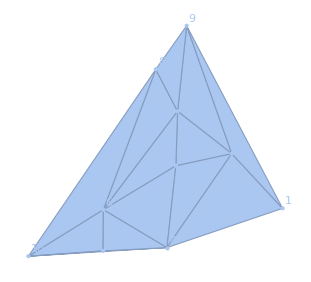

{10→3,3→6,6→10,10→4,4→3,8→6,6→2,2→8,4→6,5→6,4→5,8→10,4→7,7→5,4→1,1→7,2→7,7→9,9→2,2→5,1→9,9→8}

```mathematica
DelaunayMesh[Pin];
HighlightMesh[%,Labeled[0,"Index"]]
Ruleg=EdgeRulesMesh[%]
```

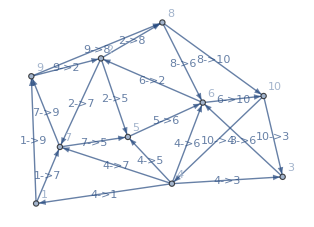

```mathematica
Gin=Graph[Ruleg,VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

```mathematica
FundLoop=FindFundamentalCycles[UndirectedGraph[Gin]];
```

```mathematica
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
```

```mathematica
RuleRevFundLoop=Table[EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],{i,Length[FundLoop]}];
```

```mathematica
h=Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[FundLoop]}] ;(* 検算済 *)
```

```mathematica
PD=PDDelaunay=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
```

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{0.660644,-0.553245,0.286914,0.926305,-1.21389,0.889127,-0.574744,0.55245,-0.757205,0.133492,0.313717,1.30003,0.924996,-0.0794436,1.65869,0.57678,-0.752107,0.829113,0.274307,-0.100781,1.08191,1.63671}

```mathematica
Gout=GDelaunay=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

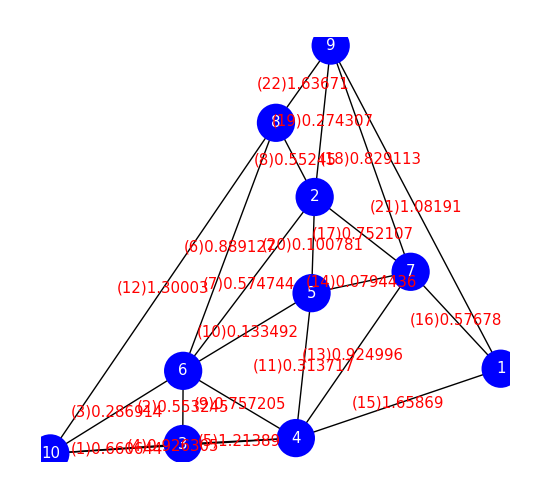

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

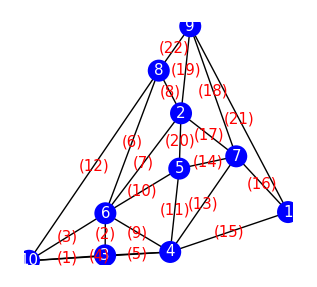

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
```

10→3 | 3→6 | 6→10 | 10→4 | 4→3 | 8→6 | 6→2 | 2→8 | 4→6 | 5→6
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

4→5 | 8→10 | 4→7 | 7→5 | 4→1 | 1→7 | 2→7 | 7→9 | 9→2 | 2→5
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

```mathematica
CurrRank=Ordering[Abs[1/Curr ]](* 昇順 *)
```

{15,22,12,5,21,4,13,6,18,9,17,1,16,7,2,8,11,3,19,10,20,14}

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{3.8125,2.51409,10.3497,5.03962,1.77094,5.65972,7.20463,2.87731,3.29034,21.343,8.83223,5.84896,4.14971,24.2069,2.4744,4.35607,3.07202,5.49906,10.5486,18.1478,6.412,1.09862}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{22,5,15,2,8,17,9,1,13,16,4,18,6,12,21,7,11,3,19,20,10,14}

```mathematica
FindShortestTour[Pin,PerformanceGoal->"Speed"]
Graphics[Line[Pin[[Last[%]]]]]
```

{26.8798,{1,7,9,8,2,5,6,10,3,4,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法4

```mathematica
GreedyDirectedPartLoop[PDCurrCostSort]
```

{8→6,6→3,3→4,4→7,7→2,2→8}

```mathematica
PartLoop1={8->6,6->3,3->4,4->7,7->2,2->8};
```

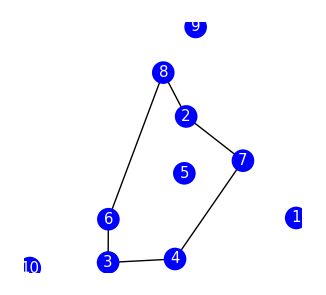

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,PartLoop1}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
Gout=Gin=GOrigin; (* 閉路、枝、点をつなぎ合わせるときは、完全グラフを想定する必要がある *)
PD=PDOrigin;
```

```mathematica
InsertVertex[PartLoop1,5]
```

{8→6,6→3,3→4,7→2,2→8,4→5,5→7}

```mathematica
PartLoop2={8->6,6->3,3->4,7->2,2->8,4->5,5->7};
```

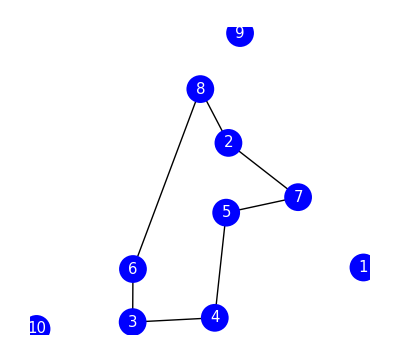

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,PartLoop2}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
Gout=Gin=GDelaunay; 
PD=PDDelaunay;
```

```mathematica
GreedyDirectedPartLoop[CurrRank]
```

{4→1,1→9,9→8,8→10,10→4}

```mathematica
PartLoop1={4->1,1->9,9->8,8->10,10->4};
```

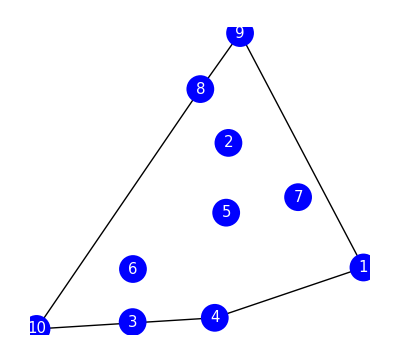

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,{4->1,1->9,9->8,8->10,10->4}}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
ContinuousInsertVertexLoop[PartLoop1]
```

{{4→1,1→9,9→8,8→10,10→4},{4→1,1→9,9→8,8→10,10→3,3→4},{4→1,9→8,8→10,10→3,3→4,1→7,7→9},{4→1,9→8,10→3,3→4,1→7,7→9,8→6,6→10},{4→1,9→8,10→3,3→4,1→7,8→6,6→10,7→2,2→9}}

```mathematica
PartLoop2={4->1,9->8,10->3,3->4,1->7,8->6,6->10,7->2,2->9};
```

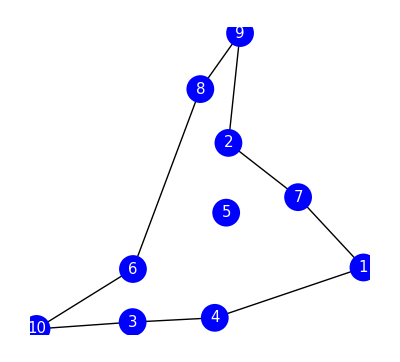

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,PartLoop2}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

#### 重み付け

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{126.499,5.5,154.663,94.0068,72.624,209.66,184.315,97.17,39.9,214.976,57.1183,73.5532,61.701,66.1105,44.7214,177.565,235.659,201.881,118.4,73.4784,36.,119.429,51.6888,38.3214,34.6133,29.5743,85.7418,104.398,7.2,57.8799,107.534,225.101,106.29,86.6637,149.316,19.0919,506.67,98.1134,66.9167,42.9009,64.622,196.499,120.459,99.0568,192.212,45.8394,66.7943,349.429,173.411,38.9297,150.52,87.5857,36.2039,46.9574,98.387,121.488,93.6,80.5929,139.101,11.2,7.82624,88.5076,178.88,89.4296,35.3344,68.0312,71.1376,67.723,75.7005,34.8827,90.3515,108.539,91.2735,42.8803,37.3352,24.1495,9.1,72.3038,617.92,107.746,57.6999,43.7049,19.799,24.8204,48.0755,58.6415,17.,92.1954,60.1684,74.3135,155.871,43.5412,18.,151.724,93.1174,193.605,166.619,25.4912,109.544,59.403,44.1816,52.4168,26.3044,44.8219,81.4985,62.482,14.1421,14.4,12.,14.7078,39.538,140.242,69.2682,127.562,128.625,20.5061,24.7,110.549,28.4605,157.08,43.6394,161.127,229.137,59.8,152.928,216.479,111.554,36.0555,94.0394,46.2,226.653,112.559,82.404,63.263,21.2132,113.564,40.1462,158.288,402.576,74.3328}

```mathematica
PDCurrCostSort
```

{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
PDWeightCurrRank=Ordering[Abs[PDWeight/Curr]]
```

{61,108,60,29,116,135,133,109,92,140,132,130,53,107,125,110,117,113,115,114,46,98,36,74,67,104,137,83,105,64,89,2,54,121,119,70,106,103,87,77,82,124,112,52,129,101,25,136,62,58,102,39,66,128,118,38,131,122,127,40,75,69,34,68,100,9,63,26,14,99,35,50,126,24,138,80,65,15,120,84,30,55,139,123,111,95,71,11,47,73,23,86,93,32,85,27,88,72,21,20,134,45,12,8,42,13,5,41,4,97,33,76,90,43,96,56,31,3,16,28,51,44,91,49,22,19,57,94,59,10,7,37,79,18,17,1,81,48,6,78}

```mathematica
GreedyDirectedPartLoop[PDWeightCurrRank]
```

{20→2,2→29,29→20}

```mathematica
PartLoop1={20->2,2->29,29->20}
```

{20→2,2→29,29→20}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
EdgeRules[Gout][[{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}]]
```

{51→46,2→16,11→32,22→2,2→11,22→1,35→20,9→34,48→8,34→21,32→2,34→50,1→2,35→36,8→1,29→35,16→29,35→3,50→21,27→51,23→48,32→27,11→46,3→22,28→22,46→27,6→23,47→51,27→6,12→47,7→48,16→21,30→34,51→12,49→9,16→9,48→26,21→35,3→28,38→9,16→50,28→31,50→9,5→49,26→7,20→22,46→5,48→6,12→5,46→12,36→3,49→30,1→48,27→48,5→38,8→22,21→36,15→37,31→22,1→27,21→29,14→25,10→49,9→30,47→18,36→28,6→47,37→17,30→10,5→15,31→8,23→7,17→4,36→31,15→44,46→32,31→26,24→6,37→5,16→38,4→18,16→11,17→47,1→32,25→24,38→49,26→8,44→37,41→19,44→17,45→33,26→43,18→25,13→41,43→24,11→38,20→3,33→39,13→40,19→42,47→4,39→34,5→11,18→14,41→40,6→14,25→13,37→12,24→14,18→13,43→7,18→6,33→10,12→17,40→42,43→23,24→23,30→39,4→13,45→44,42→44,6→51,4→41,39→10,10→15,42→45,40→45,45→15,40→33,42→17,42→4,19→40,25→43,4→19,43→13,49→15,15→33}

#### PartLoopを含まず閉路を作る

```mathematica
EdgeNumList[DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],VertexList[PartLoop1]]]
```

{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
OutEdgeRank1={61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78};
```

```mathematica
GreedyDirectedPartLoop[OutEdgeRank1]
```

{51→46,46→27,27→51}

```mathematica
Clear[OutLoop,OutEdgeRank]
```

```mathematica
OutLoop={PartLoop1};
OutEdgeRank={PDCurrCostSort};
For[j=1,j<8,j++,
OutEdgeRank=Append[OutEdgeRank,EdgeNumList[DelEdgeVertexList[EdgeRules[Gout][[OutEdgeRank[[j]]]],VertexList[OutLoop[[j]]]]]];
OutLoop=Append[OutLoop,GreedyDirectedPartLoop[OutEdgeRank[[j+1]]]]
]
```

```mathematica
OutEdgeRank=Append[OutEdgeRank,EdgeNumList[DelEdgeVertexList[EdgeRules[Gout][[OutEdgeRank[[8]]]],VertexList[OutLoop[[8]]]]]]
```

{{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,108,64,105,104,137,67,136,106,52,122,118,46,29,53,127,98,101,109,63,130,121,102,110,119,107,82,54,70,34,138,99,66,83,120,139,25,117,40,100,103,14,123,32,26,95,80,71,50,30,124,24,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,64,137,67,136,52,122,118,46,29,53,127,63,130,121,119,82,54,70,34,138,99,66,83,120,139,25,117,40,100,14,123,32,26,95,80,71,50,30,124,24,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,137,67,136,122,118,46,29,127,130,121,119,82,34,138,99,83,120,139,25,117,40,100,14,123,32,26,95,80,71,30,124,24,45,75,88,11,87,27,111,42,86,23,2,20,77,15,8,47,84,96,9,5,13,85,43,3,56,16,31,41,12,33,91,28,4,49,44,94,10,22,19,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,137,67,136,122,118,46,29,127,130,121,119,34,138,83,120,139,25,117,40,14,123,32,26,80,71,30,124,24,45,75,88,11,87,27,111,42,23,2,20,77,15,8,47,84,96,9,5,13,85,43,3,56,16,31,41,12,33,28,4,49,44,10,22,19,7,21,37,76,79,18,17,1,48,6,57,78},{92,116,137,67,136,122,118,46,29,127,130,121,119,138,120,139,117,40,14,123,32,71,30,124,45,88,11,87,27,111,42,2,20,77,15,8,47,84,96,9,5,13,43,3,56,16,41,12,33,28,4,49,44,10,22,19,7,21,37,79,18,17,1,48,6,57},{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,30,124,88,87,111,2,20,77,8,84,96,9,5,3,28,4,49,10,22,19,7,21,37,79,18,17,1,6,57},{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}}

```mathematica
OutLoop=Append[OutLoop,GreedyDirectedPartLoop[OutEdgeRank[[9]]]]
```

Part::partw: {92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}の部分28は存在しません．

Part::pkspec1: 式{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}⟦28⟧は部分指定に使用できません．

FindCycle::graph: FindCycle[Graph[{11→32,22→1,35→36,8→1,35→3,3→22,28→22,16→21,21→35,28→31,16→38,16→11,45→33,33→39,43→23,40→45,{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,«90»}⟦«1»⟦28⟧⟧}],∞,All]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[Graph[{11→32,«15»,{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,«90»}⟦{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}⟦28⟧⟧}]]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[∞]の位置1にはグラフオブジェクトが想定されています．

{{20→2,2→29,29→20},{51→46,46→27,27→51},{9→34,34→50,50→9},{48→26,26→7,7→48},{49→30,30→10,10→49},{5→15,15→37,37→5},{6→47,47→18,18→25,25→24,24→6},{17→4,4→13,13→41,41→19,19→42,42→44,44→17},EdgeRules[Graph[{11→32,22→1,35→36,8→1,35→3,3→22,28→22,16→21,21→35,28→31,16→38,16→11,45→33,33→39,43→23,40→45,{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}⟦28⟧⟧}]]}

```mathematica
Length[{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}]
```

27

```mathematica
OutLoop
```

{{20→2,2→29,29→20},{51→46,46→27,27→51},{9→34,34→50,50→9},{48→26,26→7,7→48},{49→30,30→10,10→49},{5→15,15→37,37→5},{6→47,47→18,18→25,25→24,24→6},{17→4,4→13,13→41,41→19,19→42,42→44,44→17}}

```mathematica
Flatten[OutLoop]
```

{20→2,2→29,29→20,51→46,46→27,27→51,9→34,34→50,50→9,48→26,26→7,7→48,49→30,30→10,10→49,5→15,15→37,37→5,6→47,47→18,18→25,25→24,24→6}

```mathematica
line1=Table[Line[Pin[[VertexList[{i}]]]],{i,Flatten[OutLoop]}]
```

{Line[{{57,58},{49,49}}],Line[{{49,49},{58,48}}],Line[{{58,48},{57,58}}],Line[{{30,40},{32,39}}],Line[{{32,39},{30,48}}],Line[{{30,48},{30,40}}],Line[{{52,33},{61,33}}],Line[{{61,33},{56,37}}],Line[{{56,37},{52,33}}],Line[{{25,55},{27,68}}],Line[{{27,68},{17,63}}],Line[{{17,63},{25,55}}],Line[{{48,28},{58,27}}],Line[{{58,27},{51,21}}],Line[{{51,21},{48,28}}],Line[{{40,30},{36,16}}],Line[{{36,16},{32,22}}],Line[{{32,22},{40,30}}],Line[{{21,47},{25,32}}],Line[{{25,32},{17,33}}],Line[{{17,33},{7,38}}],Line[{{7,38},{8,52}}],Line[{{8,52},{21,47}}]}

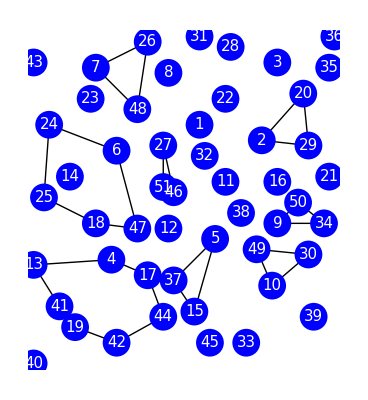

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,Flatten[OutLoop]}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,{2->29,29->20,20->2,51->46,2->16,11->32,22->2,2->11,22->1,35->20,9->34,48->8,34->21,32->2,34->50,1->2,35->36,8->1,29->35,16->29,35->3,50->21,27->51,23->48,32->27,11->46,3->22,28->22,46->27,6->23,47->51,27->6,12->47,7->48,16->21,30->34,51->12,49->9,16->9,48->26,21->35,3->28,38->9,16->50,28->31,50->9,5->49,26->7,20->22,46->5,48->6,12->5,46->12,36->3,49->30,1->48,27->48,5->38,8->22}}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

Table::iterb: 反復演算…は適正な範囲を持ちません．

-Graphics-

```mathematica
OutEdgeRank
```

{{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{NotFound,NotFound}}

```mathematica
OutLoop
```

{{2→29,29→20,20→2},EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦NotFound⟧}]]}

```mathematica
OutLoop={PartLoop1}
```

{{2→29,29→20,20→2}}

```mathematica
OutEdgeRank={PDCurrCostSort}
```

{{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}}

```mathematica
OutEdgeRank[[1]]
```

{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
OutEdgeRank
```

{{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}}

```mathematica
OutLoop
```

{{2→29,29→20,20→2},334,EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,80,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦1⟧}]]}
 |  |  |  |

```mathematica
OutLoop[[2]]
```

EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦NotFound⟧}]]

```mathematica
OutLoop[[3]]
```

EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦{{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{NotFound,NotFound},{{}⟦1⟧,NotFound}}⟧}]]

```mathematica
OutEdgeRank[[3]]
```

{{}⟦1⟧,NotFound}